## Fourier Series

Here are some useful formulae:

f(x)=a_0/2+∑_(n=1)^∞ (a_n cos(nx)+b_n sin(nx)) ⟺{a_0=1/π∫_-π^π f(x)ⅆx
a_n=1/π∫_-π^π cos(nx)f(x)ⅆx
b_n=1/π∫_-π^π sin(nx)f(x)ⅆx

f(x)==∑_(n=-∞)^∞ f_n ⅇ^(ⅈ n x)  ⟺ {f_0=1/(2π)∫_-π^π f(x)ⅆx
f_n=1/(2π)∫_-π^π f(x)ⅇ^(-ⅈ nx)ⅆx

### Orthogonality

Use Manipulate and Plot to visualise sin(n x) sin(m x) over (c-π,c+π) where c ranges from 0 to π and m,n=1,2,3. Use Filling to fill under the curve to the axis. Explain how your visualisation supports the orthogonality integral

∫_(c-π)^(c+π) sin(n x) sin(m x)ⅆx==0, n≠m  [2 Marks]

Solution

```mathematica
Manipulate[Plot[{0,sin(n x) sin(m x)},{x,-π+c,π+c},Filling->{1->{{2},{Yellow,Orange}}},PlotRange->{{-π,2π},{-1,1}}],{c,0,π},{n,Range[3]},{{m,2},Range[3]}]
```

When n≠m the area above the axis bounded by the curve equals that below, so the integral vanishes. This result holds independently of c; as c increases the part of the curve removed from left-hand end, is moved to the right-hand end.

Use Mathematica to verify the orthogonality integrals

∫_-π^π sin(n x) sin(m x)ⅆx==π δ_(n,m)
∫_-π^π cos(n x) cos(m x)ⅆx==π δ_(n,m)
∫_-π^π sin(n x) cos(m x)ⅆx==0

where δ_(n,m) is the Kronecker delta, which equals 1 if m==n, and is 0 otherwise, and m,n∈ℤ. [3 Marks]

Hint: One approach to computing the integral when m==n is to compute the result for arbitrary m and n and then take the limit as m→n.

Solution

The first integral is immediate:

```mathematica
∫_-π^π sin(mx)cos(nx)ⅆx
```

0

This follows because sin(mx) is an odd function and cos(nx) is even.

Consider the second integral:

```mathematica
∫_-π^π sin(mx)sin(nx)ⅆx
```

(2 n sin(π m) cos(π n)-2 m cos(π m) sin(π n))/(m^2-n^2)

Assuming that m≠n, the numerator vanishes (since sin(π n)==0 for n∈ℤ):

```mathematica
Simplify[%,{m,n}∈ℤ]
```

0

For m==n we need to take a limit:

```mathematica
lim_(m->n) %%
```

π-(sin(2 π n))/(2 n)

This simplifies for n∈ℤ

```mathematica
Simplify[%,n∈ℤ]
```

π

The same treatment works for the other orthogonality integral:

```mathematica
∫_-π^π cos(mx)cos(nx)ⅆx
```

(2 m sin(π m) cos(π n)-2 n cos(π m) sin(π n))/(m^2-n^2)

```mathematica
Simplify[%,{m,n}∈ℤ]
```

0

```mathematica
lim_(m->n) %%
```

(sin(π n) cos(π n))/n+π

```mathematica
Simplify[%,n∈ℤ]
```

π

Verify that ∫_0^(2π) ⅇ^(ⅈ (m-n) x) ⅆx==2π m,n where m,n∈ℤ. [2 Marks]

Solution

First a direct solution using Mathematica.

For m≠n,

```mathematica
Simplify[∫_0^(2 π) ⅇ^(ⅈ (m-n) x)ⅆx,{m,n}∈ℤ]
```

0

For m==n:

```mathematica
∫_0^(2 π) 1ⅆx
```

2 π

Alternatively, integration of exponential functions is easy:

```mathematica
∫ⅇ^(ⅈ (m-n) x)ⅆx
```

-(ⅈ ⅇ^(ⅈ x (m-n)))/(m-n)

Substituting in the limits of integration:

```mathematica
(%/.x->π)-(%/.x->-π)
```

(ⅈ ⅇ^(-ⅈ π (m-n)))/(m-n)-(ⅈ ⅇ^(ⅈ π (m-n)))/(m-n)

Express ⅇ^(ⅈ θ) as cos(θ)+ⅈ sin(θ):

```mathematica
ExpToTrig[%]
```

(2 sin(π (m-n)))/(m-n)

Clearly, for m≠n, the denominator is not zero. Also sin(n π)==0 for n∈ℤ, so this expression vanishes.

```mathematica
Simplify[%,{m,n}∈ℤ]
```

0

For m→n, compute the limit:

```mathematica
lim_(m->n) %%
```

2 π

This result is easy to see, if you recall that

```mathematica
lim_(x->0) (sin(x))/x==1
```

True

and note that

```mathematica
2π ((sin((m-n) π))/((m-n)π))==(2 sin((m-n) π))/(m-n)
```

True

### Simple Examples

Compute the Fourier series expansion of the simple function

```mathematica
f(x_):=sin(x-c)
```

where c is arbitrary, using equation (DisplayFormulaNumbered). Verify that your expansion is correct. Hint: You will need to take a limit when computing a_1 and b_1. [2 Marks]

Solution

Determine the coefficients:

```mathematica
a/:Subscript[a, 0]=1/π∫_-π^π f(x) ⅆx
```

0

In general:

```mathematica
1/π∫_-π^π f(x) cos(n x)ⅆx
```

(2 n sin(c) sin(π n))/(π (n^2-1))

```mathematica
a/:Subscript[a, n_]=Simplify[%,n∈ℤ]
```

0

We need to take a limit as n→1.

```mathematica
a/:Subscript[a, 1]=lim_(n->1) %%
```

-sin(c)

Similarly for b_n:

```mathematica
1/π∫_-π^π f(x) sin(n x)ⅆx
```

-(2 cos(c) sin(π n))/(π (n^2-1))

```mathematica
b/:Subscript[b, n_]=Simplify[%,n∈ℤ]
```

0

```mathematica
b/:Subscript[b, 1]=lim_(n->1) %%
```

cos(c)

Compute the Fourier series:

```mathematica
Subscript[a, 0]/2+Subscript[a, 1] cos(x)+Subscript[b, 1] sin(x)+∑_(n=2)^∞ (Subscript[a, n] cos(nx)+Subscript[b, n] sin(nx))
```

cos(c) sin(x)-sin(c) cos(x)

This is just a standard trig identity:

```mathematica
TrigReduce[%]==f(x)
```

True

Consider the Piecewise function:

```mathematica
f(x_):=Piecewise[{{-1, -π≤x≤(-3π)/4}, {2+4/π x, (-3π)/4<x ≤-π/4}, {1, -π/4<x ≤π/4}, {2-4/π x, π/4<x ≤(3π)/4}, {-1, (3π)/4<x≤π}}]
```

Visualise f(x) for x∈[-π,π]. Note that you can just enter the above definition. [1 Mark]

Compute the n^th coefficient, f_n, in the complex Fourier series expansions explicitly (calculating the integrals in equation (DisplayFormulaNumbered) directly). Explain why f_0==0. Verify that f_-n==f_n (which happens because f(x) is symmetric, that is f(-x)==f(x)). [2 Marks]

Use Manipulate or TabView to visualize the 1st, 3rd, 5th, 10th and 20th partial sums of the Fourier series expansion (DisplayFormulaNumbered) over (-2π,2π) and compare with the periodically extended form of f(x). Hint: consider f(Mod[x,2 π,-π]). [2 Marks]

Solution

Here is a plot of f(x):

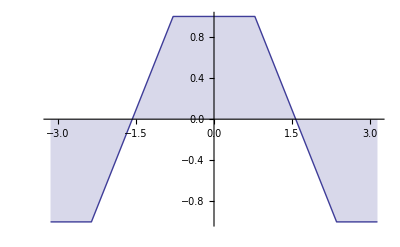

```mathematica
Plot[f(x),{x,-π,π},Filling->Axis,Exclusions->None]
```

Compute f_0:

```mathematica
f/:Subscript[f, 0]=1/(2π)∫_-π^π f(x) ⅆx
```

0

This vanishes because the function is antisymmetric about x=π/2 over (0,π) and symmetric about x=0.

Compute f_n:

```mathematica
f/:Subscript[f, n_]=FullSimplify[1/(2π)∫_-π^π f(x)ⅇ^(-ⅈ nx)ⅆx,n∈ℤ]
```

(16 sin^2((π n)/4) cos((π n)/4))/(π^2 n^2)

Verify that f_-n==f_n:

```mathematica
Subscript[f, -n]==Subscript[f, n]
```

True

Observe that f_(2n) is zero:

```mathematica
FullSimplify[Subscript[f, 2n],n∈ℤ]
```

0

Aside: It is possible to compute the Fourier series in closed-form:

```mathematica
∑_(n=-∞)^-1 Subscript[f, n] ⅇ^(ⅈ n x)+Subscript[f, 0]+∑_(n=1)^∞ Subscript[f, n] ⅇ^(ⅈ n x)
```

(2 (-2--1^(1/4) ⅇ^(-ⅈ x)+2-1^(1/4) ⅇ^(-ⅈ x)+2-(-1)^(3/4) ⅇ^(-ⅈ x)-2(-1)^(3/4) ⅇ^(-ⅈ x)))/π^2+(2 (-2--1^(1/4) ⅇ^(ⅈ x)+2-1^(1/4) ⅇ^(ⅈ x)+2-(-1)^(3/4) ⅇ^(ⅈ x)-2(-1)^(3/4) ⅇ^(ⅈ x)))/π^2

Although this expression involves complex numbers, it turns out to be real:

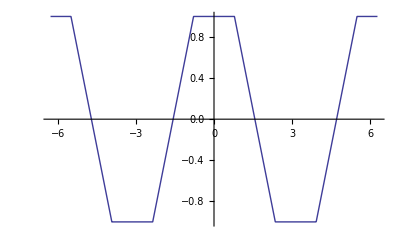

```mathematica
Plot[%,{x,-2π,2π}]
```

Partial sums of the Fourier series expansion over (-2π,2π) compared with the periodically extended form of f(x):

```mathematica
TabView[Table[k->Plot[Evaluate[{f[Mod[x,2π,-π]],∑_(n=-k)^k Subscript[f, n] Exp[ⅈ n x]}],{x,-2π,2π},PlotRange->1.3,Exclusions->None,PlotPoints->Max[{30,2k}]],{k,{1,3,5,10,20}}]]
```

12345

## Damped oscillator with periodic forcing

The differential equation for the displacement x(t) of a damped mass-spring oscillator with periodic forcing, f exp(ⅈ ω t), is

m x''(t)+b x'(t)+k x(t)==f exp(ⅈ ω t)

where m is the mass, k is the spring constant, and b is the damping coefficient. This is an inhomogenous second-order constant-coefficient differential equation, which you will have met in other mathematics courses already.

We can write

L_(b,k,m)[x][t]==f exp(ⅈ ω t)

where we have introduced the linear differential operator L_(b,k,m):

```mathematica
Subscript[L, b_,k_:1,m_:1][x_]:=t↦m x''(t)+b x'(t)+k x(t)
```

The syntax k_:1 and m_:1 assigns default values of 1 to k and m if we omit them. For example,

```mathematica
Subscript[L, b][x][t]==f exp(ⅈ ω t)
```

b x'(t)+x''(t)+x(t)==f ⅇ^(ⅈ t ω)

In this section we put f=1 and determine the periodic response to the periodic forcing exp(ⅈ ω t).

If we take the real part, we get the response to a cosine forcing, and if take the imaginary part, we get the response to a sine forcing. Why?

Enter the differential operator L_(b,k,m), defined above.

Solve the homogenous second-order constant-coefficient differential equation with b→0, k→1, m→1. The solution should look familiar. [1 Mark]

Put f→1 and compute the periodic response y(t)=A ⅇ^(ⅈ ω t) to the periodic forcing ⅇ^(ⅈ ω t).  Hint: you need to find the (complex) amplitude A. [1 Mark]

Express the squared amplitude Abs[A]^2==A^*A, which is proportional to the power in the response, as a function of b>0 and ω>0. [1 Mark]

Use Manipulate to plot the power in the response over the range 0<ω<2 as a function of b≥0. What happens to the power in the response as b increases? [2 Marks]

The resonance curves displayed in the last part of this exercise should be familiar to you from first year Physics (see also ).

Solution

Solve the homogenous second-order constant-coefficient differential equation with b→0, k→1, m→1. The solution looks familiar.

```mathematica
Subscript[L, 0][x][t]==0
```

x''(t)+x(t)==0

```mathematica
DSolve[%,x,t]
```

{{x→({t}↦c_2 sin(t)+c_1 cos(t))}}

Compute the periodic response x(t)=A ⅇ^(ⅈ ω t) to the periodic forcing ⅇ^(ⅈ ω t):

```mathematica
x(t_):=A ⅇ^(ⅈ ω t)
```

```mathematica
Subscript[L, b][x][t]==ⅇ^(ⅈ ω t)//FullSimplify
```

ⅇ^(ⅈ t ω) (1+A (-ⅈ b ω+ω^2-1))==0

```mathematica
A/.First@Solve[%,A]
```

-1/(-ⅈ b ω+ω^2-1)

Express Abs[A]^2==A*A, which is proportional to the power in the response, for b>0 and ω>0:

```mathematica
Simplify[%*%,Assumptions->{b>0,ω>0}]
```

1/((b^2-2) ω^2+ω^4+1)

Use Manipulate to plot the power in the response as a function of b over the range 0<ω<2:

```mathematica
Manipulate[Plot[1/((b^2-2) ω^2+ω^4+1),{ω,0,2},PlotRange->{0,20}],{{b,0.25},0,1}]
```

These are the resonance curves. The power drops as b increases.

## Using Fourier series for general periodic forcing

An interesting question for damped oscillators is “what is their large-time periodic response x(t) to a periodic forcing f(t)?”. Large-time means that any initial transients have died away.

We seek x(t) which solves m x''(t)+bx'(t)+k x(t)==f(t) and suppose that k is adjustable (equivalent to varying the resonant frequency, ω==√(k/m)).

For general periodic forcing f(t), represented by its (complex) Fourier series

f(t)==∑_(n=-∞)^∞ f_n ⅇ^(ⅈ n t)

we solve, one frequency mode at a time (as in Exercise Exercise), then use the principle of superposition (using linearity) to find the solution x(t):

x(t)==∑_(n=-∞)^∞ c_n ⅇ^(ⅈ n t)

### Response to periodic function:

In Exercise Exercise, you computed the (complex) Fourier coefficients f_n for the function .

In Exercise Exercise you determined the periodic response A ⅇ^(ⅈ ω t) to the periodic forcing ⅇ^(ⅈ ω t).

We are going to look at the response to the periodic driving function, , or at least a Fourier series approximation to it.

Determine the response to a single ⅇ^(ⅈ n t) term:

```mathematica
Subscript[x, n_](t_):=Subscript[c, n] ⅇ^(ⅈ n t)
```

```mathematica
Solve[Subscript[L, b,k][Subscript[x, n]][t]==ⅇ^(ⅈ n t),Subscript[c, n]]
```

{{c_n→-1/(-ⅈ b n-k+n^2)}}

In other words,

(f_n ⅇ^(ⅈ n t))_forcing⟶(f_n/((k-n^2)+ⅈ b n)ⅇ^(ⅈ n t))_response

for a single mode.

We then "superpose" (using linearity) to find the solution x(t):

x(t)==∑_(n=-∞)^∞ f_n/((k-n^2)+ⅈ b n)ⅇ^(ⅈ n t)

Consider partial sums of this solution:

x_m(t)==∑_(n=-m)^m f_n/((k-n^2)+ⅈ b n)ⅇ^(ⅈ n t)

Although these partial sums appear to be complex, because f_n=f_-n one finds that x_m(t) is real.

Use Manipulate to plot the periodic driving function, , along with the response x_m(t), over the time interval -3 π<t<3 π,  for 0.1≤k≤25, 0.001≤b≤1, and m=1,2,5,10,20. [2 Marks]

Why do you see larger responses when k≈n^2? [1 Mark]

Solution

```mathematica
Manipulate[Plot[Evaluate[{f[Mod[t,2π,-π]],∑_(n=-m)^m Subscript[f, n] ⅇ^(ⅈ n t), ∑_(n=-m)^m (Subscript[f, n] ⅇ^(ⅈ n t))/((k-n^2)+ⅈ b n)}],{t,-3 π,3 π},Ticks->{π Range[-3,3],Automatic},PlotRange->r,Exclusions->None],{k,0.1,25},{{b,0.1},0.001,1},{{m,5},{1,2,5,10,20}},{{r,2},0.,50}]
```

The response is large when k≈n^2 because (k-n^2)+ⅈ b n→ⅈ b n minimising the (absolute magnitude of the) denominator in the response sum.